# Block Arnoldi

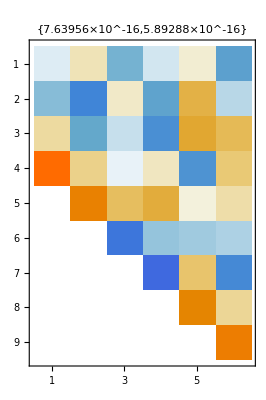

```mathematica
{m,b}={24,3};
A=RandomReal[{-1,1},{m,m}];
(* Build Q1 *)
{Q1,R1}=QRDecomposition[RandomReal[{-1,1},{m,b}]];Q1=Q1ᵀ;
(* Build Q2 *)
W=A.Q1;
(* Make perp using Gram-Schmidt *)
H11=Q1ᵀ.W; W=W-Q1.H11;
(* Make Orth using QR Decomp *)
{Q2,R2}=QRDecomposition[W];Q2=Q2ᵀ;
(* Build Q3 *)
W=A.Q2;
(* Make perp using Gram-Schmidt *)
H21=Q1ᵀ.W;H22=Q2ᵀ.W; W=W-Q1.H21-Q2.H22;
(* Make Orth using QR Decomp *)
{Q3,R3}=QRDecomposition[W];Q3=Q3ᵀ;
(* Build out bits *)
BigQ2=ArrayFlatten[{{Q1,Q2}}];
BigQ3=ArrayFlatten[{{Q1,Q2,Q3}}];
BigH=ArrayFlatten[({{H11, H21}, {R2, H22}, {0, R3}})];
MatrixPlot[BigH,
PlotLabel->Map[Norm,{A.BigQ2 -BigQ3.BigH,BigQ3ᵀ.BigQ3-IdentityMatrix[3b]}]]
```

```mathematica
Eigenvalues[BigH⟦1;;2b,1;;2b⟧]
```

{-1.05104+1.60188 ⅈ,-1.05104-1.60188 ⅈ,-1.82589+0. ⅈ,0.675212+0.79629 ⅈ,0.675212-0.79629 ⅈ,0.992495+0. ⅈ}

```mathematica
MatrixForm[Map[SingularValueList,{R1,R2,R3}]]
Eigenvalues[A,3];
Diagonal[BigH]
```

(3.04107 | 2.76131 | 2.39857
3.43009 | 2.64236 | 1.88129
3.35978 | 2.43977 | 1.81323)

{-0.0633937,-1.38982,-0.0922647,0.0972465,0.0122489,-0.149083}